```mathematica
ClearAll["Global`*"]
l = 4;
β = 0.5;
snrDB = 8;
ts =1;
snr= 10^(snrDB/20);
var=N[(l^2-1)/(6*Log[2,l]*10^(snrDB/10))];
msum = 20;
ksum = 40;
h[1] := 0;
h[-1] := 0;
h[t_]:=(Sinc[(π t)/ts] Cos[(β π t)/ts])/(1-((2 β t)/ts)^2)
g[k_,Δ_]:=g[k,Δ]=h[(k+Δ) ts]
hermite[n_,y_]:=hermite[n,y]=HermiteH[n,(y/√2)]/2^(n/2)
t[m_]:=t[m] =D[Tan[t],{t,m}]/.t->0
kappa[m_,Δ_]:=N[-(ⅈ^m)*t[m-1]*(l^m-1)/(2^m-1)*Sum[g[-k,Δ]^m + g[k,Δ]^m,{k,1,ksum}]]

alpha[0,Δ_] := 1;
alpha[2,Δ_] := 0;
alpha[4,Δ_] := kappa[4,Δ];
alpha[6,Δ_] := kappa[6,Δ];
alpha[tm_,Δ_]:=alpha[tm,Δ] = kappa[tm,Δ]+Sum[Binomial[tm-1,2*i]*kappa[tm-2*i,Δ]*alpha[2*i,Δ],{i,2,(tm/2)-2}]
sigsqr[Δ_] := sigsqr[Δ]=
N[var + 1/3*(l^2-1)*Sum[g[-k,Δ]^2+g[k,Δ]^2,{k,1,ksum}]] (*sigsqr = σ^2 = variance*)
f[y_,w0_,Δ_] :=N[1/(√(2π*sigsqr[Δ]))*Exp[(-(y-w0*g[0,Δ])^2)/(2*sigsqr[Δ])]*(1+Sum[alpha[2*m,Δ]/((2*m)!*sigsqr[Δ]^(m))*hermite[2*m,(y-w0*g[0,Δ])/(√sigsqr[Δ])],{m,2,msum}])]
```

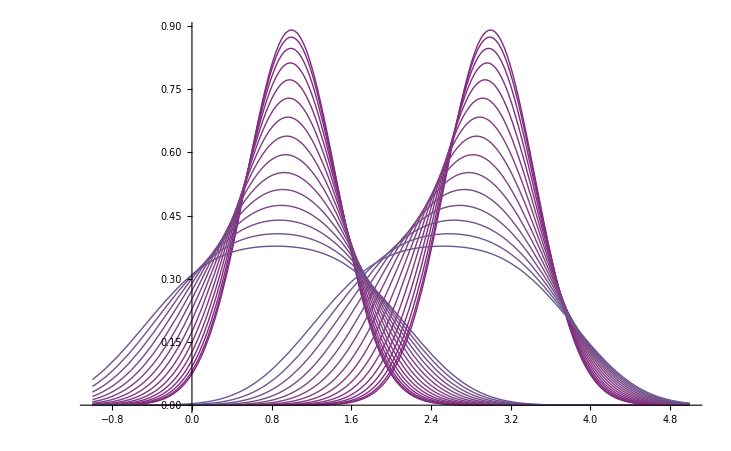

```mathematica
Plot[Evaluate[Join[Table[f[y,1,timing],{timing,0.02,0.3,0.02}],Table[f[y,3,timing],{timing,0.02,0.3,0.02}]]],{y,-1,5},ColorFunction->"Rainbow"]
```

```mathematica
Plotting the difference between P (ω = 1) and P (ω = 3) to visually show the decision region boundaries
```

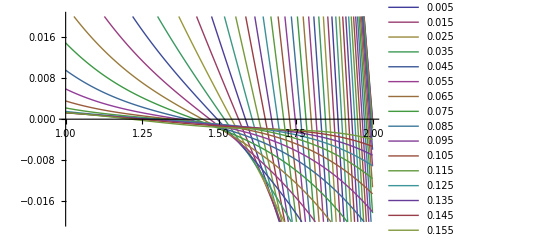

```mathematica
offvals = Range[0.005,0.495,0.01];
dpdf = ParallelTable[{y,f[y,1,toff]-f[y,3,toff]},{toff,offvals},{y,1,2,0.001}];
ListLinePlot[dpdf,PlotRange->{{1,2},{-0.02,0.02}},PlotLegends->offvals]
```

```mathematica
Here I just want to calculate the approximate decision region boundaries, and compare them to 2*g(Δ)
```

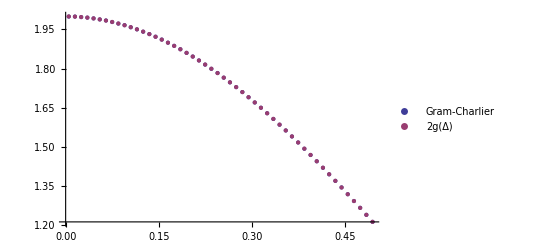

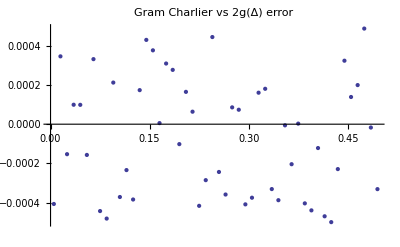

```mathematica
decregbound=1+0.001*(ParallelTable[Position[dpdf[[toff]],_?(#<0&)][[1,1]],{toff,Length[offvals]}]-1.5);estimatedrb=Table[2*h[toff],{toff,offvals}];
xydecregbound = Transpose[{offvals,decregbound}];
xyestimatedrb = Transpose[{offvals,estimatedrb}];
MatrixForm[NumberForm[Transpose[{xydecregbound,xyestimatedrb}],{4,3}]];
ListPlot[{xydecregbound,xyestimatedrb},PlotLegends->{"Gram-Charlier","2g(Δ)"}]
ListPlot[Transpose[{offvals,decregbound-estimatedrb}],PlotLabel->"Gram Charlier vs 2g(Δ) error"]
```

1.

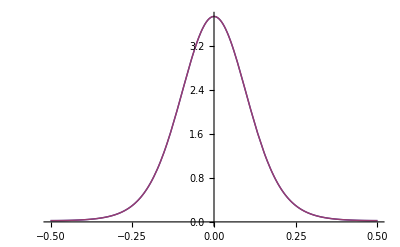

```mathematica
thikfactor[var_]:=thikfactor[var]=1/((2 π)^2 var)
thik[var_,y_]:=thik[var,y]=Exp[thikfactor[var] Cos[2 π y]]/BesselI[0,thikfactor[var]]
NIntegrate[thik[0.01,y],{y,-0.5,0.5}]
thikdist = ProbabilityDistribution[thik[0.01,y],{y,-0.5,0.5}]; 
Plot[{thik[0.01,y],PDF[thikdist,y]},{y,-0.5,0.5}]
```

Evaluating the Tikhonov distribution over finite regions and weighting the calculated decesion region boundaries accordingly.

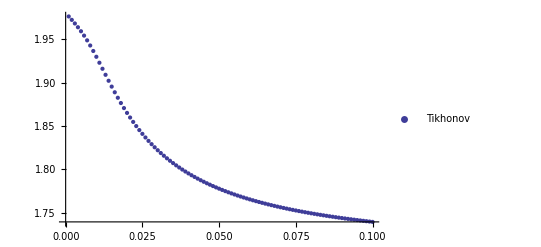

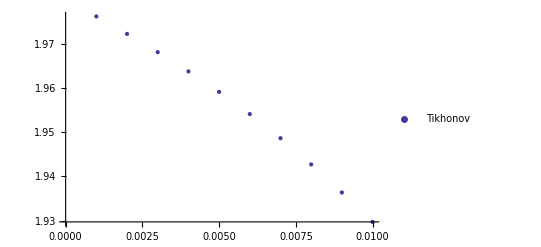

```mathematica
tvar=Range[0.001,0.1,0.001];
width=Max[offvals]/Length[offvals];
thiklist=ParallelTable[NIntegrate[thik[var,x],{x,y-width/2,width/2+y}],{var,tvar},{y,offvals}];
(*Table[2Sum[thiklist[[a,b]],{b,Length[offvals]}],{a,Length[tvar]}];
Table[NIntegrate[thik[var,x],{x,-0.5,0.5}],{var,tvar}];*)
decreg=2*(thiklist.decregbound);
xydecreg = Transpose[{tvar,decreg}];
ListPlot[{xydecreg},PlotLegends->{"Tikhonov"}]
xydecreg = Transpose[{tvar[[1;;10]],decreg[[1;;10]]}];
ListPlot[{xydecreg},PlotLegends->{"Tikhonov"},PlotStyle->PointSize[Large]]
```